```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->t]
```

```mathematica
T1[t_,m_]:= Module[{K=0*IdentityMatrix[m]},ReplacePart[K,Table[{x,x},{x,2,m,2}]->t]]
```

```mathematica
T2[t_,m_]:=t*IdentityMatrix[m]-T1[t,m]
```

```mathematica
Clear[LEFT]
```

```mathematica
LEFT[ω_,m_]:=LEFT[ω,m]=Module[{J=Inverse[β[ω,0.001,1,0,m]],A:=Inverse[β[ω,0.001,1,0,m]],Ta:=T1[1,m],Tb= T2[1,m]},Do[J=Inverse[IdentityMatrix[m]-A.Tb.Inverse[IdentityMatrix[m]-A.Ta.J.Ta].A.Tb].A,5000];J=J]
```

```mathematica
f1[y_,start_,stop_]:= Table[{x,y},{x,start,stop}]
```

```mathematica
s[xstart_,xstop_,ystart_,ystop_]:=Module[{J=f1[ystart,xstart,xstop]},Do[J=Join[f1[y,xstart,xstop],J],{y,ystart+1,ystop}];J=J]
```

```mathematica
Clear[dist]
```

```mathematica
dist[total_,concentration_,area_]:=dist[total,concentration,area]=Table[SortBy[Join[RandomSample[Join[s[1,100,1,Round[area/2]]],concentration],RandomSample[Join[s[1,100,area-Round[area/2],area]],total-concentration]],First],10000]
```

```mathematica
f[ω_,δ_,t_,ϵ_,ϵ1_,area_,total_,concentration_,number_,unitcell_]:=Inverse[Module[{J=β[ω,δ,t,ϵ,area]},Do[J=Module[{m=unitcell},If[dist[total,concentration,area][[number]][[loc1,1]]==m,ReplacePart[J,{{dist[total,concentration,area][[number]][[loc1,2]],dist[total,concentration,area][[number]][[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]]
```

```mathematica
CA[ω_,δ_,t_,ϵ_,ϵ1_,total_,concentration_,number_,size_,area_]:= Module[{},
recurs=Module[{J1=LEFT[ω,area]},
Do[
J1=Inverse[IdentityMatrix[area]-f[ω,δ,t,ϵ,ϵ1,area,total,concentration,number,unitcell+1].T2[t,area].Inverse[IdentityMatrix[area]-f[ω,δ,t,ϵ,ϵ1,area,total,concentration,number,unitcell].T1[1,area].J1.T1[1,area]].f[ω,δ,t,ϵ,ϵ1,area,total,concentration,number,unitcell].T2[t,area]].f[ω,δ,t,ϵ,ϵ1,area,total,concentration,number,unitcell+1],{unitcell,1,100,2}];J1=J1];ir=Inverse[IdentityMatrix[area]-LEFT[ω,area].T1[1,area].recurs.T1[1,area]].LEFT[ω,area];il=Inverse[IdentityMatrix[area]-recurs.T1[1,area].LEFT[ω,area].T1[1,area]].recurs;
gdd1= il-ConjugateTranspose[il];
grr1= ir-ConjugateTranspose[ir];
Gnonlocalrl=ir.T1[1,area].recurs;
GNON1= Gnonlocalrl-ConjugateTranspose[Gnonlocalrl];TRA=Abs[Tr[gdd1.T1[1,area].grr1.T1[1,area]-T1[1,area].GNON1.T1[1,area].GNON1]];If[TRA>10,10,TRA]]
```

```mathematica
Mean[ParallelTable[CA[1,0.001,1,0,1,100,50,NUM,1,15],{NUM,1000}]]
```

1.0738

```mathematica
Monitor[Table[ParallelTable[CA[1,0.001,1,0,1,x,x/2,num,1,15],{num,2000}]//Mean,{x,10,100,10}],x]
```

{4.5616,3.20377,2.27673,1.68165,1.34463,1.19299,1.10579,1.09721,1.03859,1.09141}

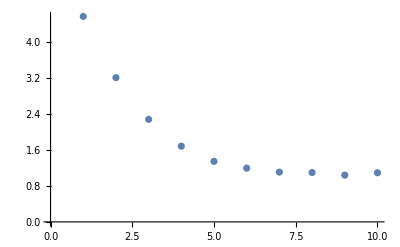

```mathematica
ListPlot[{4.561602808137281,3.203774854277006,2.2767250250533513,1.681647204905668,1.344629781587329,1.192994052124454,1.105789270478963,1.0972131398720062,1.0385853949283452,1.0914127766643689}]
```

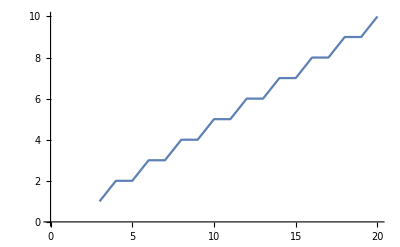

```mathematica
ListLinePlot[Monitor[Table[{m,CA[1,0.001,1,0,1,50,25,1,1,m]},{m,Range[3,20,1]}],m]]
```